# Getting Started with Mathematica

Mathematica is a powerful technical computing system with an associated programming language, the Wolfram language. In this notebook we will learn the basics of using Mathematica as a tool to study and solve Mathematical problems.

## Interacting with Mathematica

### Front End and Kernel

Mathematica has two parts:

A Front End that provides the user interface you are interacting with right now. The Front End allows you to open, edit and run a Notebook such as the one we are currently using.

A Kernel that handles commands sent from the Front End and returns results to the Front End.

A Notebook is just a file containing a hierarchy of cells. You can Open/Close/Save notebooks in the standard way using the File menu item.

Notebooks store all of the input and output but do not save the state of the Kernel. This has several consequences:

When you close a notebook and reopen it without quitting Mathematica your Kernel will still be there with the same state as before.

If you quit Mathematica (which also quits the Kernel) and reopen it later, any of the calculations and definitions you created but did not output to the notebook will not be retained.

If you have multiple notebooks open at once, by default they all talk to the same Kernel and will share definitions and values for functions and variables.

### Hello World

To get started we will issue our first command to the Front End. Place the cursor in the line below and use Shift+Return to send it to the Kernel to be executed. The result returned from the Kernel will be printed on the following line

```mathematica
1+1
```

Notice that input the line is labeled with In[1] and the output line is labeled with Out[1]. Notebooks are divided into Cells of different types. Possible types include Input, Output, Text, Section, etc. You can change the type of a cell in the Format menu bar item.

We can prevent the output from being created by putting a semicolon at the end of a line:

```mathematica
1+1;
```

### Inserting new lines

To insert a new cell anywhere, just place the cursor between two existing cells, click, and then start typing. Try adding a new input cell between this paragraph and the next one.

To delete a cell, select it on the right and press Backspace. Try deleting the new cell you created in the last step.

### Help

There are several ways to get help with using Mathematica. The Documentation Centre can be found under the menu: Help → Wolfram Documentation. This provides extensive documentation on all aspects of Mathematica. You can also find a quick explanation of a given function using ‘?’. For example, try running the following

```mathematica
?Simplify
```

## The basics

### Variables (Symbols)

In Mathematica, variables are called Symbols (there is a good reason for this as symbols are much more powerful than variables in other languages, but we will not worry about that for now). The names of symbols can contain capital and lower case letters or numbers (but must start with a letter or $).

#### Assigning values to Symbols

To assign a value to a Symbol, we can use a single = sign. Let’s start by inserting a new line and using it to set “a” to have the value “100”.

```mathematica
a=100;
```

Symbols can store numbers (integers, decimals, complex, rational) and strings (using “double quotes”) but can also be used to store other things. We will see more about this later.

#### Printing the value of a Symbol

We can output the value of a Symbol by running an input cell without the semicolon at the end. Try it.

```mathematica
a
```

### Mathematical operations

We can perform the standard Mathematical operations using the operators +, -, *, /, ^ and (). Try using Mathematica to do some calculations using these operators.

```mathematica
(1+2*(3+4)-7)^2/11
```

Note that sometimes we have to be careful about the order of operations. Mathematica follows the standard mathematical precedence rules that we learn in school (BOMDAS).

We can also input in a user-friendly mathematical notation using Ctrl-/ for divide, Ctrl-6 for power, Ctrl-2 for square root. Try to figure out how to write the following: √(x^2+y^2/z^4)

```mathematica
√(x^2+y^2/z^4)
```

There are lots of other useful shortcuts for input that we will learn along the way, many of which can be accessed using the Esc key. For example, try creating an input cell and typing Esc-pi-Esc

```mathematica
π
```

### Numerical evaluation

When we type π, we get the mathematical constant pi. Since π in an irrational number, Mathematica will just leave it as π unless we tell it that we want a numerical approximation to a given number of digits. We can do this using N[π] for a machine precision approximation or N[π, digits] for an approximation to ‘digits’ decimal places. Try evaluating π to 1000 digits

```mathematica
N[π,1000]
```

### Functions

Notice in the previous example that we had square brackets after the N. In Mathematica, square brackets (not parenthesis - that is used for precedence) are used for functions and all built-in functions start with a capital letter. Functions with multiple arguments have their arguments separated by a comma.

Here are a few examples:

```mathematica
Sqrt[4]
```

```mathematica
Sin[π]
```

```mathematica
Cos[π]
```

```mathematica
Exp[ⅈ π]
```

```mathematica
Log[2,8]
```

### Defining mathematical expressions

We said previously that Symbols can be used to store more than just numbers. One common use is to use them to store mathematical expressions. For, example, we could have the following definitions

```mathematica
a = (x+x^2)/(x Sin[y]^2+x Cos[y]^2)
```

(x+x^2)/(x Cos[y]^2+x Sin[y]^2)

```mathematica
b=x^2+1
```

1+x^2

We can then use these in place of the full expression:

```mathematica
a+3 Tan[y]^2
```

(x+x^2)/(x Cos[y]^2+x Sin[y]^2)+3 Tan[y]^2

```mathematica
b-1
```

x^2

### Substituting values into an expression with replacement rules

Note that the previous expressions were given in terms of undefined symbols “x” and “y”. Why would we want to form an expression with undefined symbols? A very common reason is that undefined symbols can be substituted out at any later time:

```mathematica
a/.x->3
```

12/(3 Cos[y]^2+3 Sin[y]^2)

Here, the arrow above is made by typing a minus sign (-) and then a greater than sign ( > ) right next to each other and then a space. Watch closely when you do it - Mathematica automatically converts it to a right arrow.

The replacement of the Symbol “x” with an actual value was performed by a combination of /. and  ...  ->  ... ; both are needed. The /. is a shorthand syntax equivalent to ReplaceAll (look it up in the documentation) and the ...→... is a Rule (again, look it up in the documentation).

It is important to understand that this substitution has not changed the value of “a” or set a value for “x” (because neither was set using “=”)

```mathematica
a
```

(x+x^2)/(x Cos[y]^2+x Sin[y]^2)

```mathematica
x
```

x

Instead the substitution merely took the definition for “a” in terms of “x” and “y”, replaced “x” with “3”, and returned the result.

We can do several substitutions at the same time by giving them as a list:

```mathematica
a/.{x->3,y->π}
```

Again, there is no change in the actual definition of “a” or “x”.

### Equations

Generally an equation involves some sort of relational operator (equal, not equal, etc.). One thing to be clear from the start: the “=” that we’ve used so far is the assignment operator and is distinct from what we’re going to talk about now. The symbol that tests equality is  ==   or (esc)==(esc).

Here is a true statement (notice the two equal signs)

```mathematica
2 *3 == 6
```

Here is another true statement:

```mathematica
2*3 > 0
```

Likewise, there are false statements

```mathematica
2*3 > 100
```

We have 6 arithmetic relational operators:  ==, !=, >,<,>= and <=. Experiment with them to check some (in)equalities of your own. You don’t need to limit yourself to only numbers in relations.

### Defining functions

Symbols have even more applications beyond being used to hold numbers and expressions. They are also used to define functions. The standard way to define a function in Mathematica is to give its name, then square brackets with the names of the arguments inside (with an underscore at the end of each argument), then ‘:=” and finally the definition of a function. If we need intermediate temporary symbols in the function we can use Module to create them. Let’s look at an example:

```mathematica
f[x_,y_,z_]:=Module[{result},
result=x^2+2x y-z^7;
result
];
```

Eventually you may learn the details about why we define functions in this way, but for now it is sufficient to just remember that this is the recommended way to define functions.

Try evaluating the function for several values of x, y and z.

```mathematica
f[3,2,1]
```

20

Try defining your own function g(x,y)=(x^2+y^2)^(1/2) and evaluate it for different values of x and y

```mathematica
g[x_,y_]:=(x^2+y^2)^(1/2);
```

```mathematica
g[1,2]
```

√5

### Arrays (Vectors, Matrices and “Tensors”)

#### Defining arrays

We define arrays (called Lists in Mathematica) using curly braces {}. For example, let us define a vector (one-dimensional array), a matrix (two dimensions) and a rank-3 “tensor”

```mathematica
v={4,7};
```

```mathematica
A={{3,6},{2,7}};
```

```mathematica
T={{{1,7},{4,5}},{{3,8},{9,2}}};
```

When printing a matrix, we can put the output in readable matrix notation using MatrixForm

```mathematica
MatrixForm[v]
```

(4
7)

```mathematica
MatrixForm[A]
```

(3 | 6
2 | 7)

```mathematica
MatrixForm[T]
```

((1
7) | (4
5)
(3
8) | (9
2))

#### Generating Arrays

Sometimes it is convenient to generate an array from a formula for the coefficients. We can use Table to achieve this. For example, let’s create a 1-D array of the numbers from 1 to 6.

```mathematica
Table[i,{i,1,6,1}]
```

Here, {i,1,6,1} is the iterator which says to increment i from 1 to 6 by steps of 1. The first argument is the function (just i in this case) and is evaluated for each case. Table make a list of the results.

Let’s try a different function with the same iterator.

```mathematica
squares=Table[i^2,{i,1,6,1}]
```

The first argument can be any expression. Try a few possibilities

```mathematica
Table[0,{i,1,6,1}]
```

```mathematica
Table[BesselJ[i,x],{i,1,6,1}]
```

#### Map

Sometimes we already have an array and we want to apply a function to each element of the array. We can achieve this using Map. Let’s try mapping the Sqrt function over our array of squares.

```mathematica
Map[Sqrt,squares]
```

You will often see a different but equivalent syntax for Map using “/@”.

```mathematica
Sqrt/@ squares
```

#### Listable functions and arrays

In many cases there is an even easier way to apply a function element-wise to elements of an array. Many built-in functions have the Listable attribute, which means that they are automatically applied to each list member without  having to use Map or other looping commands. For example, Sqrt is Listable so we have a simpler way to apply it to our array

```mathematica
Attributes[Sqrt]
```

Try passing the whole vector “squares” to the Sqrt function.

```mathematica
Sqrt[squares]
```

#### Extracting parts of arrays

We can extract parts of arrays using double square brackets [[...]]. For example, to extract the vector with components T_(1,2,i) for all i=1,2 we could use either of the following

```mathematica
T[[1,2,All]]
```

```mathematica
T[[1,2,1;;2]]
```

There are lots of different ways to specify the parts of an array that we want. For more information see the documentation for Part.

#### Multiplication of arrays

When we talk about multiplying arrays (whether they are vectors, matrices or tensors) we can actually mean several different things. The two most important possibilities are:

Standard matrix multiplication. We do this using the “dot product”, which in Mathematica is given by “.”.

```mathematica
A.v
```

{54,57}

Element-wise multiplication. This is what we get if use times, “*”.

```mathematica
A*A
```

{{9,36},{4,49}}

```mathematica
v*v
```

{16,49}

```mathematica
T*T
```

{{{1,49},{16,25}},{{9,64},{81,4}}}

### Associations

The final type of object we will find useful is the Association, which we can think of as an array with non-numeric keys for indexing.

#### Defining associations

To define an association we use <| ..-> ... |>. For example

```mathematica
assoc=<|"key1"->2,3->11,"keyx"->7|>;
```

#### Accessing elements in associations

To access a given named element in an association we use single square brackets and the name of the key (a bit like functions)

```mathematica
assoc["keyx"]
```

7

## Doing mathematics with Mathematica

### Plotting functions

One of the best ways to understand a function is to plot it. For example, we can use Plot to produce a plot of a function of one variable. Try it for f(x)=x^2.

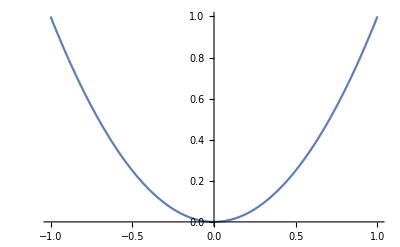

```mathematica
Plot[x^2,{x,-1,1}]
```

To plot functions of two variable, one approach is to consider it as a surface embedded in three-dimensional space using Plot3D. Try using Plot3D to plot the function sin(x+y^2) for x∈[-3,3] and y∈[-2,2].

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

3D plots are interactive. Try clicking and dragging around to rotate the plot.

Sometimes we want to do something similar, but slightly different. Consider a 3D vector x⃗(u,v). We can think of this as a defining parametric two-dimensional surface in 3D. To visualise this we use ParametricPlot3D. Let’s try it with the Klein bottle defined as follows:

```mathematica
klein[u_,v_]:={Cos[u](3+Cos[u/2]Sin[v]-Sin[u/2]Sin[2v]),Sin[u](3+Cos[u/2]Sin[v]-Sin[u/2]Sin[2v]),Sin[u/2]Sin[v]+Cos[u/2]Sin[2v]};
```

```mathematica
ParametricPlot3D[klein[u,v],{u,0,2Pi},{v,0,2Pi}]
```

-Graphics3D-

There are many many more plotting functions available. We won’t review them here, but you can get an idea by checking the Help pages for all functions including Plot in the name:

```mathematica
?*Plot*
```

### Manipulate-ing visualitions

Sometimes we want to plot a function over a range of values for a parameter. We can achieve this using Manipulate:

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

### Simplification

One of the most powerful uses of Mathematica is as a symbolic algebra tool. Let’s see how we can use it to simplify functions.

Obvious factors in fractions are automatically cancelled

```mathematica
a=((x-2)(x+3))/((x-2)(x-9))
```

Sometimes it’s not so obvious (to us or to Mathematica) that there is a common factor to be cancelled.

```mathematica
a=(x^2+x-6)/(x^2-11x+18)
```

In those cases, Simplify will often spot the cancellation and produce a simplified expresssion

```mathematica
Simplify[a]
```

Simplify also knows about the properties of many built-in functions. For example, it knows all the standard rules of trigonometry.

```mathematica
b = (x+x^2)/(x Sin[y]^2+x Cos[y]^2)
```

```mathematica
Simplify[b]
```

Other useful functions for simplification include: FullSimplify, Factor, Expand, Apart, Together, Cancel and Collect. Look them up in the documentation to learn what each one does.

### Differentiation

Another thing we can do with symbolic algebra is to compute the derivative of a function using D[...]. Let’s try a few examples

```mathematica
a = x^2+3x+4 y^2
```

```mathematica
D[a,x]
```

```mathematica
D[a,y]
```

```mathematica
D[ArcSinh[x],x]
```

### Integration

As well as differentiation, the other natural thing we might want to do is integrate a function. Mathematica knows about how to integrate all sorts of functions, and has most identities from textbook tables of integrals built-in. Let’s look at a few examples

```mathematica
a = x/(x^2+2x+1);
Integrate[a,x]
```

```mathematica
b=Integrate[Sin[x],{x,0,3}]
```

Sometimes operations will return non-elementary functions:

```mathematica
Integrate[Cos[x Cos[2 π t]],{t,0,1}, Assumptions->x>0]
```

BesselJ[0,x]

#### Numerical Integration

Sometimes, there is no known analytic solution to an integral and we need to resort to a numerical approximation using NIngegrate.

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,2}]
```

1.24706

### Sums

Similar to integration, we can also compute sums (both infinite and not) using Sum. Let’s see a few examples

```mathematica
Sum[1/n^2,{n,1,∞}]
```

```mathematica
Sum[(-1)^n/n,{n,1,∞}]
```

```mathematica
Sum[ (-1)^k x^(2k)/(k!)^2,{k,0,∞}]
```

BesselJ[0,2 x]

### Series expansions

We can compute power series expansions of an expression using Series

```mathematica
Series[Sin[x]/x,{x,0,20}]
```

1-x^2/6+x^4/120-x^6/5040+x^8/362880-x^10/39916800+x^12/6227020800-x^14/1307674368000+x^16/355687428096000-x^18/121645100408832000+x^20/51090942171709440000+O[x]^21

In some cases this is just the normal Taylor series

```mathematica
Series[f[x+Δx],{Δx,0,2}]
```

f[x]+f'[x] Δx+1/2 f''[x] Δx^2+O[Δx]^3

In other cases, we get more general series such as a Laurent series

```mathematica
Series[Csc[x],{x,0,2}]
```

1/x+x/6+O[x]^3

### Special Functions

We saw in the previous examples of integration and sums that sometimes we can produce special functions such as the Bessel function. Mathematica has knowledge of a large library of special functions and we can treat them as we would any function. We can plot them

```mathematica
Plot[BesselJ[0,x],{x,0,10}]
```

We can find series expansions

```mathematica
Series[BesselJ[0,x],{x,0,10}]
```

We can integrate them

```mathematica
Integrate[BesselJ[0,x],{x,0,∞}]
```

and differentiate them

```mathematica
D[BesselJ[0,x],x,x]
```

For more details on the the extensive list of functions known by Mathematica see the documentation tutorial on Mathematical Functions.

### Solving equations

We can solve many different types of equations. For example, a system of linear equations

```mathematica
Solve[{
2x+y-z==8,
-3x-y+2z==-11,
-2x+y+2z==-3},
{x,y,z}]
```

{{x→2,y→3,z→-1}}

or a quadratic

```mathematica
Solve[(x-2)(x+3)==0,x]
```

or higher order polynomials

```mathematica
Solve[16 x^9-x(3 x^2-1)(12 x^6-(3 x^2-1)^2)==0,x]
```

{{x→-1},{x→0},{x→1},{x→-1/(√5)},{x→1/(√5)},{x→-√(3/8-(ⅈ √7)/8)},{x→√(3/8-(ⅈ √7)/8)},{x→-√(3/8+(ⅈ √7)/8)},{x→√(3/8+(ⅈ √7)/8)}}

or systems of polynomials

```mathematica
Solve[{x^2-3 y^2==0,y^3+2 x^2==0},{x,y}]
```

or even more complicated equations

```mathematica
Solve[Sin[θ]^2-Cos[θ]^2==0,θ]
```

### Differential equations

Lastly, we can also solve differential equations (both ordinary and partial). Let’s look at some examples.

#### Ordinary Differential Equations

```mathematica
s=NDSolveValue[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

InterpolatingFunction[…]

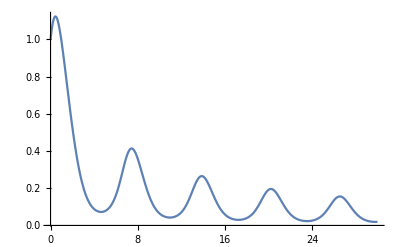

```mathematica
Plot[s[x],{x,0,30},PlotRange->All]
```

#### Partial Differential Equations

```mathematica
sol2D=NDSolveValue[{D[ϕ[t,x],t]==D[ϕ[t,x],x,x],ϕ[0,x]==ⅇ^(-x^2),ϕ[t,-20]==ϕ[t,20]},ϕ,{t,0,2},{x,-20,20}]
```

InterpolatingFunction[…]

```mathematica
Animate[Plot[sol2D[t,x],{x,-50,50},PlotRange-> {{-20,20},{0,1}}],{t,0,2,0.01}]
```

```mathematica
sol3D=NDSolveValue[{D[ϕ[t,x,y],t,t]==D[ϕ[t,x,y],x,x]+D[ϕ[t,x,y],y,y]/2+(1-ϕ[t,x,y]^2)(1+2ϕ[t,x,y]),ϕ[0,x,y]==ⅇ^(-(x^2+y^2)),ϕ[t,-5,y]==ϕ[t,5,y],ϕ[t,x,-5]==ϕ[t,x,5],Derivative[1,0,0][ϕ][0,x,y]==0},ϕ,{t,0,4},{x,-5,5},{y,-5,5}];
```

```mathematica
Manipulate[Plot3D[sol3D[t,x,y],{x,-5,5},{y,-5,5},PlotRange->All,ImageSize->200,Mesh->All],{t,0,4},SynchronousUpdating->True]
```

### Units

```mathematica
dist=UnitConvert[Quantity[18, "Kilometers"],"cm"]
```

1800000 cm

```mathematica
UnitConvert[dist,"light year"]
```

5/2627980686828 ly

### “Computable data”

#### Graphs

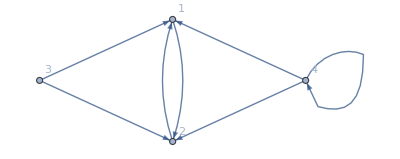

```mathematica
GraphPlot[{1->2,2->1,3->1,3->2,4->1,4->2,4->4},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
GraphPlot[Table[i->Mod[i^2,234],{i,300}]]
```

-Graphics-

```mathematica
CommunityGraphPlot[ExampleData[{"NetworkGraph","DolphinSocialNetwork"}]]
```

-Graphics-

#### Financial Data

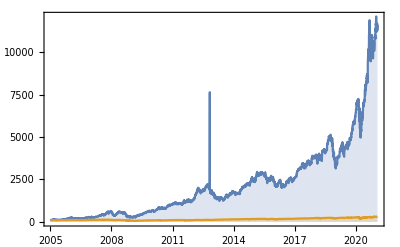

```mathematica
DateListPlot[{FinancialData["AAPL","CumulativeFractionalChange",{2005}],FinancialData["SP500","CumulativeFractionalChange",{2005}]},Joined->True,Filling->Bottom,PlotRange->All]
```

#### Historical data

```mathematica
eclipse=SolarEclipse[DateObject[{2017,8,1,0,0}],"TotalPhasePolygon",EclipseType->"Total"];
GeoGraphics[{Red,eclipse},GeoProjection->"Equirectangular"]
```

-Graphics-

```mathematica
eclipse=SolarEclipse[DateObject[{1999}],"TotalPhasePolygon",EclipseType->"Total"];
GeoGraphics[{Red,eclipse},GeoProjection->"Equirectangular"]
```

-Graphics-

#### Demographic data

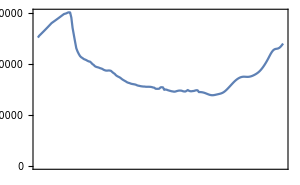

```mathematica
DateListPlot[CountryData["Ireland",{{"Population"},{1800,2018}}],ImageSize->300]
```

#### Model fitting

Imagine we have some data taken from an experiment and we would like to find a model that fits the data well. To start, let’s make up some data to use:

```mathematica
data=Table[Sqrt[x] Cos[x]+RandomReal[{-1,1}],{x,100}];
```

If we have a good idea for a model that might fit the data, then we can use FindFit to look for the parameters that best fit the data

```mathematica
model=a1 x^a2 Cos[a3 x]/.FindFit[data,a1 x^a2 Cos[a3 x],{a1,a2,a3},x]
```

1.10384 x^0.475768 Cos[1.00018 x]

Now let’s plot the model against the data

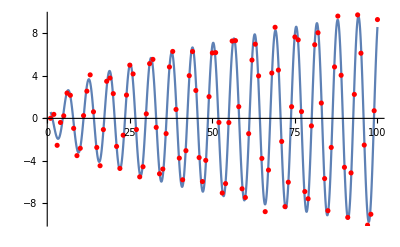

```mathematica
Show[Plot[model,{x,1,100}],ListPlot[data,PlotStyle->Red]]
```

#### Image identification (using neural networks)

Later in this module we will build a neural network model that can recognise features in images. Mathematica has sophisticated versions of these models built in. For example, ImageIdentify will try to produce a description of the contents of an image.

```mathematica
ImageIdentify[-Graphics-]
```

hound

```mathematica
ImageIdentify[-Graphics-,Entity["Species","Infraspecies:CanisLupusFamiliaris"]]
```

beagle

```mathematica
ImageIdentify[-Graphics-]
```

hound

```mathematica
ImageIdentify[-Graphics-]
```

domestic cat

```mathematica
ImageIdentify[-Graphics-]
```

sail

```mathematica
ImageIdentify[-Graphics-]
```

domestic pig

```mathematica
ImageIdentify[-Graphics-]
```

Hello Kitty